```mathematica
rk3RK4[f_,a_,b_,y0_,n_]:=Module[{h=(b-a)/(n-1),xi={},yi={y0},punkty={},bledy={}, xi3={},yi3={y0},punkty3={}, bledy3={}},
For[i=1,i≤n,i++,
t=a+((i-1)*h);
AppendTo[xi,t];
AppendTo[xi3,t];
];
For[i=2,i≤n,i++,
k1=h*(f[xi[[i-1]],yi[[i-1]]]);
k2=h*(f[xi[[i-1]]+h/2,yi[[i-1]]+k1/2]);
k3=h*(f[xi[[i-1]]+h/2,yi[[i-1]]+k2/2]);
k4=h*(f[xi[[i-1]]+h,yi[[i-1]]+k3]);

k31=h*(f[xi3[[i-1]],yi3[[i-1]]]);
k32=h*(f[xi3[[i-1]]+h/2,yi3[[i-1]]+k31/2]);
k33=h*(f[xi3[[i-1]]+h/2,yi3[[i-1]]+k32/2]);

kr4=(k1+2*k2+2*k3+k4 )/6;
kr3=(k31+4*k32+k33 )/6;
s4=N[yi[[i-1]]+kr4];
s3 = N[yi3[[i-1]]+kr3];
AppendTo[yi,s4];
AppendTo[yi3,s3];
];
For[i=1,i≤n,i++,
v4={xi[[i]],yi[[i]]};
v3={xi3[[i]],yi3[[i]]};
AppendTo[punkty,v4];
AppendTo[punkty3,v3];
];
dots4=ListPlot[punkty,PlotStyle->{PointSize[.02],Green}];
dots3=ListPlot[punkty3,PlotStyle->{PointSize[.02],Red}];
rd=DSolve[{y'[x]==f[x,y[x]],y[a]==y0},y[x],x][[1,1,2]];
For[i=1,i≤n,i++,
fff4=N[Abs[(rd/.x->xi[[i]])-yi[[i]]]];
fff3=N[Abs[(rd/.x->xi3[[i]])-yi3[[i]]]];
w4={xi[[i]],fff4};
w3={xi3[[i]],fff3};
AppendTo[bledy,w4];
AppendTo[bledy3,w3];
];
dot1=ListPlot[bledy,PlotStyle->{PointSize[.005],Green},Joined->True];
dot2=ListPlot[bledy,PlotStyle->{PointSize[.005],Black}];
dot3=ListPlot[bledy3,PlotStyle->{PointSize[.005],Blue},Joined->True];
dot4=ListPlot[bledy3,PlotStyle->{PointSize[.005],Black}];
wyk=Plot[rd,{x,a,b}];
GraphicsGrid[{{Show[wyk,dots4,dots3,AxesLabel->{HoldForm[x],HoldForm[y]},PlotLabel->"Rysunek1",LabelStyle->{Gray},PlotRange->All]},{Show[dot1,dot2,dot3,dot4,AxesLabel->{HoldForm[x],HoldForm[y]},PlotLabel->"Rysunek2",LabelStyle->{Gray},PlotRange->All]}},
ImageSize->Large]
];
```

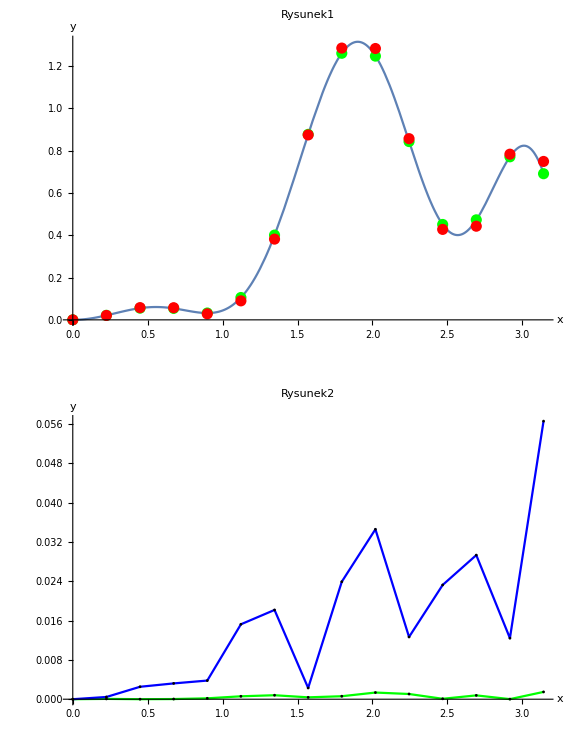

```mathematica
f[x_, y_] :=E^x Sin[x]Cos[2 x]^2 - 3 y;
rk3RK4[f, 0, π, 0, 15]
```

```mathematica
DSolve[{y'[x]==f[x,y[x]],y[a]==y0},y[x],x][[1,1,2]]
```

-1/69700 ⅇ^(-3 x) (-69700 ⅇ^(3 a) y0-2050 ⅇ^(4 a) Cos[a]+2091 ⅇ^(4 a) Cos[3 a]-2125 ⅇ^(4 a) Cos[5 a]+2050 ⅇ^(4 x) Cos[x]-2091 ⅇ^(4 x) Cos[3 x]+2125 ⅇ^(4 x) Cos[5 x]+8200 ⅇ^(4 a) Sin[a]-2788 ⅇ^(4 a) Sin[3 a]+1700 ⅇ^(4 a) Sin[5 a]-8200 ⅇ^(4 x) Sin[x]+2788 ⅇ^(4 x) Sin[3 x]-1700 ⅇ^(4 x) Sin[5 x])